```mathematica
NotebookEvaluate["~/Documents/Sparse\ Grids/Checking\ SBP/Methods\ and\ Functions\ for\ SBP.nb"]
```

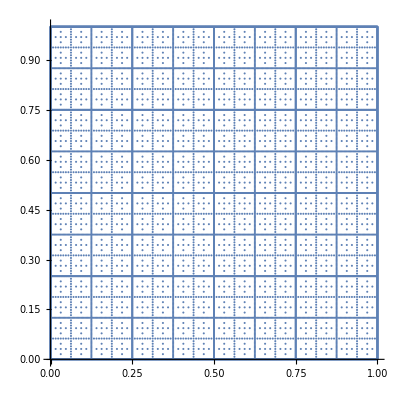

```mathematica
ListPlot[Flatten[makeSparse[10],3],AspectRatio->1]
```

```mathematica
Table[switch3[kx,i]switch3[ky,j]/.kx->3/.ky->3,{i,0,8},{j,0,8}]//MatrixForm
```

(1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64
-1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64
1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64 | -1/64 | 1/64)

```mathematica
showWeights[n_]:=Sum[Sum[Table[weights1D[i,Max[0,getrow[perp,diag]],n]weights1D[j,Max[0,getcol[perp,diag]],n],{i,0,2^n},{j,0,2^n}],{perp,-1,endperp[diag]}],{diag,-1,n}]
```

```mathematica
showFullWeights[lx_,ly_]:=Sum[Table[weights1D[i,kx,lx] weights1D[j,ky,ly],{i,0,2^lx},{j,0,2^ly}],{kx,0,lx},{ky,0,ly}]
```

```mathematica
showWeights[6]//MatrixPlot
```

```mathematica
weights1D[i_,kx_,lx_]:=If[Mod[i,2^(lx-kx)]==0,switch3[kx,2^(kx-lx)i],0]
```

```mathematica
Table[switch3[1,i],{i,0,8}]
```

{-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2,1/2,-1/2}

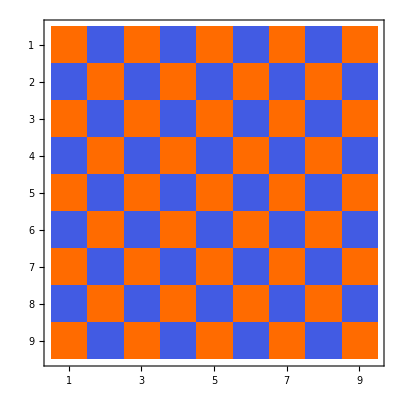

```mathematica
Table[switch3[1,i]switch3[1,j],{i,0,2^3},{j,0,2^3}]//MatrixPlot
```

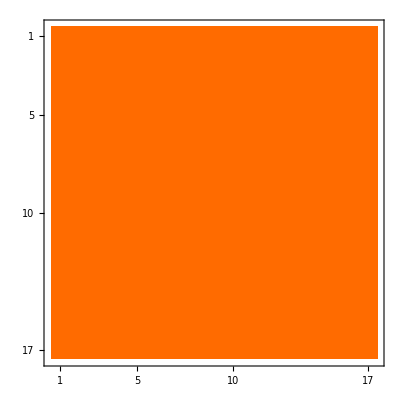

```mathematica
showWeights[5]//MatrixPlot
```